```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQp[n_]:=If[PrimeQ[n]&&n>0,True,False]
```

# Analytic Number Theory

Arithmetic

## Division

## Greatest Common Divisor

## Prime Numbers

### Prime Gap size n

#### Example

```mathematica
ClearAll[f,g,h,h1,h2]
f[n_]:=Product[Prime[k],{k,1,n}]
g[n_]:=Table[{f[n]+2+k,FactorInteger[f[n]+2+k]},{k,0,n-1}]
h[n_]:=Table[{n!+2+k,FactorInteger[n!+2+k]},{k,0,n-1}]
h1[n_,m_]:=Table[{k+1,n!+2+k,FactorInteger[n!+2+k]},{k,0,m-1}]
h2[n_,m_]:=Select[Table[{k+1,n!+2+k,PrimeQ[n!+2+k]},{k,0,m-1}],#[[3]]==True&]
h2[19,100]//TableForm
FactorInteger[19!+1]
```

88 | 121645100408832089 | True

{{71,1},{1713311273363831,1}}

## Fundamental Theorem of Arithmetic

## Euclidean Algorithm

Tools

## Abel Summation

### Discrete Version

#### Example

```mathematica
ClearAll[a,f,s,A,abelSum];
a[r_]:=r/2
A[n_]:=Sum[a[k],{k,1,n}]
f[r_]:=r+1
s[n_]:=Sum[a[k]f[k],{k,1,n}]
abelSum[m_,n_]:=Sum[A[k](f[k]-f[k+1]),{k,m-1,n-1}]+A[n]f[n]-A[m-1]f[m-1]
abelSum[1,x]//Simplify;
Table[{s[k],abelSum[1,k],1/6 k (2+3 k+k^2)},{k,1,7}]//tf
```

1 | 1 | 1
4 | 4 | 4
10 | 10 | 10
20 | 20 | 20
35 | 35 | 35
56 | 56 | 56
84 | 84 | 84

### Continuous Version

#### [ToDo] Example ( Setup via Ram Murty methode: verbeteren, want klopt niet! )

```mathematica
(1/2 x^2+1/2 x)(1/2 x+1/2)//Expand
```

x/4+x^2/2+x^3/4

```mathematica
Integrate[(t^2+t)/4,{t,1,x}]
```

-5/24+x^2/8+x^3/12

```mathematica
x/4+x^2/2+x^3/4-(-5/24+x^2/8+x^3/12)
```

5/24+x/4+(3 x^2)/8+x^3/6

```mathematica
ClearAll[f]
f[x_]:=5/24+x/4+(3 x^2)/8+x^3/6
f[6]//N
```

51.2083

Arithmetic Functions and Dirichlet Series

### Multiplicative Functions

#### Example

The Prime Number Theorem

Dirichlet’s Theorem

Error Estimates and the Riemann Hypothesis

Temp

## Tmp-1

```mathematica
Product[Sin[(π k/n)],{k,1,n-1}]
```

2^(1-n) n

```mathematica
Product[Gamma[k/n+1]/(k/n),{k,1,n-1}]//(TraditionalForm[Sqrt[#^2]]&)
```

√((2 π)^(n-1)/n)

```mathematica
ClearAll[Li];
Li[x_]:=Integrate[1/Log[y],{y,2,x}]
Li[20.]//N
```

8.86014

```mathematica
LogIntegral[20.]-LogIntegral[2.]
```

8.86014

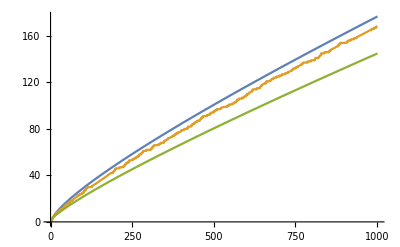

```mathematica
Plot[{LogIntegral[y]-LogIntegral[2],PrimePi[y],y/Log[y]},{y,2,1001},AxesOrigin->{0,0}]
```

## Tmp-2

```mathematica
ClearAll[f,tmp];
f[]:=Module[{s,s1,s2,k,l,a,b,from,to,c},
s={};
k=401;
While[k<800,
a=k;b=800-k;
If[PrimeQ[a]&& PrimeQ[b],
s=AppendTo[s,{a,b}]];
k=k+1;];
s1={};
s2={};
l=1;
While[l<Length[s]+1,
a=s[[l,1]];
b=s[[l,2]];
from=a-b+1;
to=a+b;
While[from<to,
c=from;
If[PrimeQ[c]&& PrimeQ[a+b-c]&& PrimeQ[a+c-b]&& PrimeQ[b+c-a]&& PrimeQ[a+b+c],
s1=AppendTo[s1,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}]];
s2=AppendTo[s2,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}];
from=from+1;
];
l=l+1];
s1]
tmp=f[]//tf
```

577 | 223 | 797 | 3 | 1151 | 443 | 1597
643 | 157 | 797 | 3 | 1283 | 311 | 1597
757 | 43 | 797 | 3 | 1511 | 83 | 1597
787 | 13 | 797 | 3 | 1571 | 23 | 1597

```mathematica
ClearAll[f,tmp];
f[]:=Module[{s,s1,s2,k,l,a,b,from,to,c},
s={};
k=401;
While[k<800,
a=k;c=800-k;
If[PrimeQ[a]&& PrimeQ[c],
s=AppendTo[s,{a,c}]];
k=k+1;];
s1={};
s2={};
l=1;
While[l<Length[s]+1,
a=s[[l,1]];
c=s[[l,2]];
from=a-c+1;
to=a+c;
While[from<to,
b=from;
If[PrimeQ[b]&& PrimeQ[a+b-c]&& PrimeQ[a+c-b]&& PrimeQ[b+c-a]&& PrimeQ[a+b+c],
s1=AppendTo[s1,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}]];
s2=AppendTo[s2,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}];
from=from+1;
];
l=l+1];
s1]
tmp=f[]//tf
```

577 | 797 | 223 | 1151 | 3 | 443 | 1597
643 | 797 | 157 | 1283 | 3 | 311 | 1597
757 | 797 | 43 | 1511 | 3 | 83 | 1597
787 | 797 | 13 | 1571 | 3 | 23 | 1597

```mathematica
ClearAll[f,tmp];
f[n_]:=Module[{s,s1,s2,k,l,a,b,from,to,c},
s={};
k=Floor[n/2]+1;
While[k<n,
a=k;b=n-k;
If[PrimeQ[a]&& PrimeQ[b],
s=AppendTo[s,{a,b}]];
k=k+1;];
s1={};
s2={};
l=1;
While[l<Length[s]+1,
a=s[[l,1]];
b=s[[l,2]];
from=a-b+1;
to=a+b;
While[from<to,
c=from;
If[PrimeQ[c]&& PrimeQ[a+b-c]&& PrimeQ[a+c-b]&& PrimeQ[b+c-a]&& PrimeQ[a+b+c],
s1=AppendTo[s1,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}]];
s2=AppendTo[s2,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}];
from=from+1;
];
l=l+1];
s1]
tmp=f[800]//tf
Map[PrimeQ[#]&,tmp]
```

577 | 223 | 797 | 3 | 1151 | 443 | 1597
643 | 157 | 797 | 3 | 1283 | 311 | 1597
757 | 43 | 797 | 3 | 1511 | 83 | 1597
787 | 13 | 797 | 3 | 1571 | 23 | 1597

True | True | True | True | True | True | True
True | True | True | True | True | True | True
True | True | True | True | True | True | True
True | True | True | True | True | True | True

```mathematica
tmp=f[400]//tf
Map[PrimeQ[#]&,tmp]
```

233 | 167 | 397 | 3 | 463 | 331 | 797
263 | 137 | 397 | 3 | 523 | 271 | 797
317 | 83 | 397 | 3 | 631 | 163 | 797
347 | 53 | 397 | 3 | 691 | 103 | 797

True | True | True | True | True | True | True
True | True | True | True | True | True | True
True | True | True | True | True | True | True
True | True | True | True | True | True | True

```mathematica
ExtendedGCD[577,223]
ExtendedGCD[233,167]
```

{1,{-80,207}}

{1,{-43,60}}

```mathematica
(1/2 x^2+1/2 x)(1/2 x+1/2)//Expand
```

x/4+x^2/2+x^3/4

```mathematica
Integrate[(t^2+t)/4,{t,1,x}]
```

-5/24+x^2/8+x^3/12

```mathematica
x/4+x^2/2+x^3/4-(-5/24+x^2/8+x^3/12)
```

5/24+x/4+(3 x^2)/8+x^3/6

```mathematica
ClearAll[f]
f[x_]:=5/24+x/4+(3 x^2)/8+x^3/6
f[6]//N
```

51.2083

```mathematica
LiouvilleLambda[1271+12345I]
```

-1

```mathematica
FactorInteger[1271+12345I,GaussianIntegers->True]
```

{{1+ⅈ,1},{9+4 ⅈ,1},{860+233 ⅈ,1}}

```mathematica
-I (1+I)(2+3I)
```

5+ⅈ

```mathematica
{PrimeNu[2^11],PrimeNu[2 3^7],PrimeNu[2^5 3 5]}
{PrimeNu[2^11 103],PrimeNu[2 3^7 107],PrimeNu[2^5 3 5  101]}
```

{1,2,3}

{2,3,4}

```mathematica
ClearAll[f]
f[t_]:=Log[t]
f'[t]
```

1/t

```mathematica
Integrate[t-1/2,{t,1,x}]//Simplify
```

1/2 (1-2 x+x^3)

```mathematica
FindSequenceFunction[Table[Integrate[Floor[n*x],{x,0,1}],{n,20}],n]
```

1/2 (-1+n)

```mathematica
Integrate[t+1/2,{t,1,x}]//Simplify
```

1/2 (-2+x+x^2)

```mathematica
Limit[Integrate[1/t^2,{t,1,x},Assumptions->{x>1}],x->Infinity]
```

1

```mathematica
Total[MangoldtLambda[Divisors[10000]]]
```

4 Log[2]+4 Log[5]

```mathematica
Log[2]+Log[5]//N
Log[10]//N
```

2.30259

2.30259

```mathematica
ⅇ^(4 Log[2]+4 Log[5])
```

10000

```mathematica
16*625
```

10000

```mathematica
11^2+12^2-16^2
11^2+13^2-17^2
```

9

1

```mathematica
121-289
```

-168

```mathematica
√(102^2+105^2-107^2+20)
```

100

```mathematica
12^2+15^2-17^2
```

80

```mathematica
17^2
```

289

```mathematica
FactorInteger[220]
```

{{2,2},{5,1},{11,1}}

```mathematica
ClearAll[f]
f[n_]:=Select[Table[k^2-n,{k,1,16}],#>0&]
f[4]
Divisors[f[3]]//tf
```

{5,12,21,32,45,60,77,96,117,140,165,192,221,252}

1 |  |  |  |  |  |  | 
1 | 2 | 3 | 6 |  |  |  | 
1 | 13 |  |  |  |  |  | 
1 | 2 | 11 | 22 |  |  |  | 
1 | 3 | 11 | 33 |  |  |  | 
1 | 2 | 23 | 46 |  |  |  | 
1 | 61 |  |  |  |  |  | 
1 | 2 | 3 | 6 | 13 | 26 | 39 | 78
1 | 97 |  |  |  |  |  | 
1 | 2 | 59 | 118 |  |  |  | 
1 | 3 | 47 | 141 |  |  |  | 
1 | 2 | 83 | 166 |  |  |  | 
1 | 193 |  |  |  |  |  | 
1 | 2 | 3 | 6 | 37 | 74 | 111 | 222
1 | 11 | 23 | 253 |  |  |  |

```mathematica
14^2-13
```

183

```mathematica
(1-183)/2
```

-91

```mathematica
14^2+91^2-92^2
```

13

```mathematica
36-23
```

13

```mathematica
6^2+6^2-7^2
```

23

```mathematica
7^2+11^2-12^2
```

26

```mathematica
EulerPhi[30]
```

8

```mathematica
Map[EulerPhi[#]&,Divisors[6]]
```

{1,1,2,2}

```mathematica
Total[Divisors[100]]
```

217

```mathematica
Floor[√150]
```

-38

```mathematica
ClearAll[f];
f[n_]:=(Binomial[(n+1)!+n,n]-1)/((n+1)!)-(n+1)Floor[(Binomial[(n+1)!+n,n]-1)/((n+1)(n+1)!)]
```

```mathematica
f[1]
f[2]
f[3]
f[4]
```

1

3/2

11/6

25/12

```mathematica
HarmonicNumber[4]
```

25/12